# NEAT

студент 3 курса 5 группы
Лицкевич Данила
20-12-2020

# NEAT

## 0. Info

https://towardsdatascience.com/neat-an-awesome-approach-to-neuroevolution-3eca5cc7930f

## Generating individual old

Гаплоидный генотип. Фазовое пространство данной задачи состоит из особей, характеризующихся одиннадцатью признаками {α_i}∈ℝ^11, каждый из которых задаёт некий угол в градусах. 
α_1 — угол наклона головы, изменяется в пределах -90°⩽α_1⩽+90 °;
α_2 — угол наклона корпуса, изменяется в пределах -45°⩽α_2⩽+180 °;

Точность α_1:Δx <1° ⟹ Y > 180° ⟹ bits > 8       Δx ≈0.703125

### Nodes

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

Input — количество входов - fixed;
Output — количество выходов - fixed;
Hidden — количество скрытых нейронов - 0 ≤ Hidden ≤ Total-Input-Output;
Total — количество нейронов - 0 ≤ Total ≤ 255;

Точность Total:Δx =1  ⟹ bits = 8

```mathematica
Nodes[in_,out_,hidden_]:=Flatten[{ConstantArray["I",in],ConstantArray["O",out],ConstantArray["H",hidden]}]
```

### Connections

Input — нейрон входа - 0 ≤ Total ≤ 255;
Output — нейрон выхода - 0 ≤ Total ≤ 255;
weight — количество скрытых нейронов -90 ≤ weight ≤ +90 ;
enabled — активирована ли связь - 0 ≤ enabled ≤ 1;
inovation — активирована ли связь - 0 ≤ enabled ≤ 1;

Точность Input:Δx =1  ⟹ bits = 8       
Точность Output:Δx =1  ⟹ bits = 8       
Точность weight:Δx <0.1  ⟹ bits = 11     ⟹   Δx =180/2048≂0.0878906

Точность α_1:Δx <1° ⟹ Y > 180° ⟹ bits > 8       Δx ≈0.703125

Точность Total:Δx =1 ⟹ Y > 180° ⟹ bits = 8

Точность Total:Δx =1 ⟹ Y > 180° ⟹ bits = 8

```mathematica
Connection[in_,out_,weight_,enabled_,inovation_]={}
```

## 1. Individuals

## Generating Population

### Nodes

#### kmNode

```mathematica
kmActivationFunc[id_]:=
Switch[id,
0, #&,
1,Tanh[#]&,
2,LogisticSigmoid[#]&,
3,Sin[#]&,
4,UnitStep[#]&,
5,Ramp[#]&
]
```

#### kmNode

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
ClearAll[kmNode]
kmNode[id_,level_,totalFuncs_:5]:=<|
"nodeId"->id,
"level"->level,
"inputSum"->0,
"bias"->RandomReal[{-1,1}],
"activationFunc"->RandomInteger[totalFuncs],
"output"->0
|>
```

```mathematica
kmNodeOutput[node_,prevNodes_]:=
Join[node,<|"inputSum"->#,"output"->node["bias"]+kmActivationFunc[node["activationFunc"]][#]|>]&[Total[prevNodes⟦All,"output"⟧]]
```

```mathematica
kmNode[1]
kmNodeOutput[%,{kmNode[2]~Join~<|"output"->12|>,kmNode[3]~Join~<|"output"->2|>}]
```

<|nodeId→1,inputSum→0,bias→-0.856647,activationFunc→0,output→0|>

<|nodeId→1,inputSum→14,bias→-0.856647,activationFunc→0,output→13.1434|>

### Connections

```mathematica
CantorPairing[x_,y_]:=((x+y)(x+y+1))/2+y
```

#### kmConnection

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
kmConnection[{in_,out_},weight_:1]:=<|
"input"->in,
"output"->out,
"weight"->RandomReal[{-weight,weight}],
"enabled"->True,
"inovation"->CantorPairing[in,out]
|>
```

### Individual

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

```mathematica
ClearAll[kmAddIndividual]
SetAttributes[kmAddIndividual,HoldFirst]
kmAddIndividual[population_,hidden_:0]:=
AppendTo[population["individuals"],
<|
"input"->population["input"],
"output"->population["output"],
"total"->population["input"]+population["output"],
"nodes"->Join[
kmNode[#,1,0]&/@Range[population["input"]],
kmNode[#,2]&/@(population["input"]+Range[population["output"]])
],
"connections"->(kmConnection[#]&/@
Flatten[
Outer[
{#1,#2}&,
Range[population["input"]],
Range[population["input"]+1,population["input"]+population["output"]]
],1])
|>]
```

### Inovations

#### kmInovation (*toDelete*)

```mathematica
kmInovation[in_,out_]:=<|
"input"->in,
"output"->out,
"inovation"->CantorPairing[in,out]
|>
```

### Population

Input — количество входов;
Output — количество выходов;

```mathematica
kmPopulation[in_,out_,options___]:=<|
"input"->in,
"output"->out,
"best"-><||>,
(*"inovations"->{},*)
"individuals"->{}
|>~Join~options
```

### Connection' s logics

#### kmFindNode

```mathematica
kmFindNode[individual_,id_]:=
FirstPosition[individual["nodes"],<|"nodeId"->id,___|>]
```

```mathematica
kmFindNode[testPop["individuals"]⟦1⟧,2]
```

{2}

```mathematica
testPop[["individuals",1,"nodes",kmFindNode[testPop["individuals"]⟦1⟧,2]]]=1
```

#### kmInNodes

Finds all nodes which are  IN nodes for the node

```mathematica
kmInNodes[nodeId_,connections_]:=
Reap[
If[nodeId==#["output"],Sow[#["input"]]]&/@connections;
]//Last//Last
```

```mathematica
kmInNodes[2,{kmConnection[{1,2}],kmConnection[{3,2}]}]
```

{1,3}

#### kmExistConnectionQ

```mathematica
kmExistConnectionQ[connection:{in_,out_},connections_]:= 
Or@@({#["input"],#["output"]}==connection&/@connections)
```

### kmAddConnection

```mathematica
SetAttributes[kmAddConnection,HoldFirst]
kmAddConnection[population_,individualId_,conn:{in_,out_}]:= 
Block[{
individual=population["individuals"]⟦individualId⟧
},
individual⟦"connections"⟧=Join[
individual["connections"],
If[individual["nodes"]⟦in,"level"⟧<individual["nodes"]⟦out,"level"⟧,{kmConnection[conn]},{}]
];
population⟦"individuals", individualId⟧=individual
]
```

### kmAddNode

```mathematica
SetAttributes[kmAddNode,HoldFirst]
kmAddNode[population_,individualId_,connectionId_]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
connection, oldOutNodePos
},
connection=individual["connections"]⟦connectionId⟧;
individual⟦"connections",connectionId,"enabled"⟧=False;

oldOutNodePos=kmFindNode[individual,connection["output"]];
individual⟦"total"⟧+=1;
individual⟦"nodes"⟧=
Append[individual["nodes"],kmNode[individual["total"],individual⟦"nodes",oldOutNodePos,"layer"⟧]];
individual⟦"nodes",oldOutNodePos,"layer"⟧+=1;

individual⟦"connections"⟧=Join[
{kmConnection[{connection["input"],#}],
kmConnection[{#,connection["output"]}]}&[individual["total"]],
individual["connections"]
];
population⟦"individuals", individualId⟧=individual
]
```

```mathematica
kmAddNode[testPop,1,1]
```

<|input→2,output→3,total→6,nodes→{<|nodeId→1,level→1,inputSum→0,bias→0.107872,activationFunc→0,output→0|>,<|nodeId→2,level→1,inputSum→0,bias→-0.578445,activationFunc→0,output→0|>,<|nodeId→3,level→2,inputSum→0,bias→-0.14451,activationFunc→4,output→0|>,<|nodeId→4,level→2,inputSum→0,bias→0.799849,activationFunc→5,output→0|>,<|nodeId→5,level→2,inputSum→0,bias→0.876759,activationFunc→4,output→0|>,kmNode[6]},connections→{<|input→1,output→6,weight→0.682336,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.734594,enabled→True,inovation→48|>,<|input→1,output→3,weight→-0.617162,enabled→False,inovation→13|>,<|input→1,output→4,weight→-0.192583,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.529421,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.538147,enabled→True,inovation→18|>,<|input→2,output→4,weight→-0.286403,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.982429,enabled→True,inovation→33|>}|>

### Tests

```mathematica
testPop=kmPopulation[2,3]
kmAddIndividual[testPop]
```

<|input→2,output→3,best→<||>,individuals→{}|>

{<|input→2,output→3,total→5,nodes→{<|nodeId→1,level→1,inputSum→0,bias→0.107872,activationFunc→0,output→0|>,<|nodeId→2,level→1,inputSum→0,bias→-0.578445,activationFunc→0,output→0|>,<|nodeId→3,level→2,inputSum→0,bias→-0.14451,activationFunc→4,output→0|>,<|nodeId→4,level→2,inputSum→0,bias→0.799849,activationFunc→5,output→0|>,<|nodeId→5,level→2,inputSum→0,bias→0.876759,activationFunc→4,output→0|>},connections→{<|input→1,output→3,weight→-0.617162,enabled→True,inovation→13|>,<|input→1,output→4,weight→-0.192583,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.529421,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.538147,enabled→True,inovation→18|>,<|input→2,output→4,weight→-0.286403,enabled→True,inovation→25|>,<|input→2,output→5,weight→0.982429,enabled→True,inovation→33|>}|>}

```mathematica
Dynamic@testPop
```

## Individual decoding

#### kmNodesLayers

```mathematica
ClearAll[kmNodesLayers]
kmNodesLayers[individual_]:=
Module[
{},

Function[]
]
```

```mathematica
kmNodesLayers[testPop[["individuals",1]]]
```

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Function[]

#### kmIndividualToFunction

```mathematica
ClearAll[kmIndividualToFunction]
kmIndividualToFunction[individual_]:=
Module[
{},

Function[]
]
```

```mathematica
kmIndividualToFunction[testPop[["individuals",1]]]
```

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Function[]

## Population viewing (realisatoin Delayed)

```mathematica
testIndividual=<|"input"->2,"output"->3,"hidden"->4,"connections"->{<|"input"->1,"output"->5,"weight"->-0.9628618224751473,"enabled"->1,"inovation"->1|>,<|"input"->3,"output"->4,"weight"->0.22393191857363837,"enabled"->1,"inovation"->2|>,<|"input"->4,"output"->6,"weight"->-0.4785485230617863,"enabled"->1,"inovation"->3|>,<|"input"->6,"output"->5,"weight"->0.45075859641862426,"enabled"->1,"inovation"->4|>,<|"input"->8,"output"->5,"weight"->0.5039873848534051,"enabled"->1,"inovation"->5|>}|>;
```

### Individual viewing

#### kmNodes

1  – in node
2  – out node
3  – hidden node

```mathematica
kmNodes[type_,nodesQuant_,level_]:=
{Switch[type,1,Red,2,Blue,3,Gray,True,Black],Disk[{-nodesQuant+2#,level},0.25]&/@Range[nodesQuant]}
```

#### kmViewIndividual

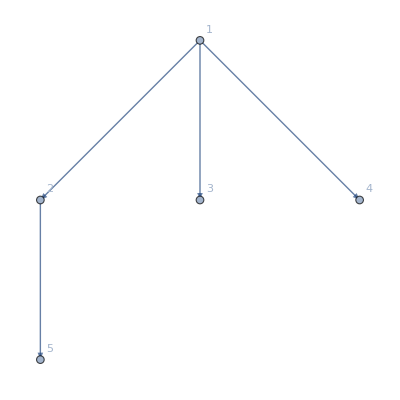

```mathematica
TreeGraph[{1->2,1->3,1->4,2->5},EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow",VertexLabels->"Name"]
```

```mathematica
kmViewIndividual[individ_]:=
Graphics[{kmNodes[1,3,1],kmNodes[2,2,2]}]
```

```mathematica
Dynamic@kmViewIndividual[1]
```

```mathematica
Graph
```

### Population viewing

## Population mutations

```mathematica
<|"a"->2,"v"->3|>~Join~<|"a"->324|>
```

<|a→324,v→3|>